## Chemical data

```mathematica
SetDirectory[NotebookDirectory[]<>"../pics"]
```

/home/jam/Kuweta/mma_lessons/pics

```mathematica
ChemicalData["Caffeine","Formula"]
```

C_8H_10N_4O_2

```mathematica
caffDiag=ChemicalData["Caffeine","StructureDiagram"];caffDiagColor=ChemicalData["Caffeine","ColorStructureDiagram"];
```

```mathematica
Export["06-caffeine-structure.pdf",caffDiag]
```

06-caffeine-structure.pdf

```mathematica
Export["06-caffeine-structure-color.pdf",caffDiagColor]
```

06-caffeine-structure-color.pdf

```mathematica
ChemicalData["Caffeine","MoleculePlot"]
```

```mathematica
caffMolec=ImageCrop[
Rasterize[
ChemicalData["Caffeine","MoleculePlot"],RasterSize->800]
]
```

```mathematica
Export["06-caffeine-molecule.pdf",caffMolec]
```

06-caffeine-molecule.pdf

```mathematica
ChemicalData["Caffeine","Phase"]
```

solid

```mathematica
ChemicalData["Water","Phase"]
```

liquid

```mathematica
ChemicalData["Water","MoleculePlot"]
```

-Graphics3D-

```mathematica
Entity["Element","Iron"]["Dataset"]
```

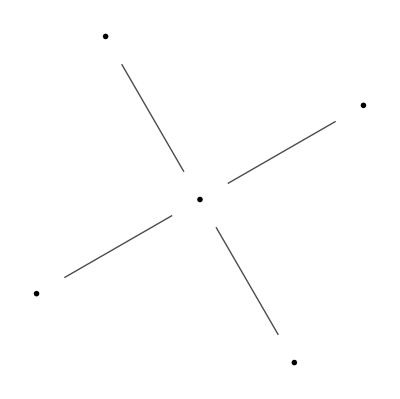
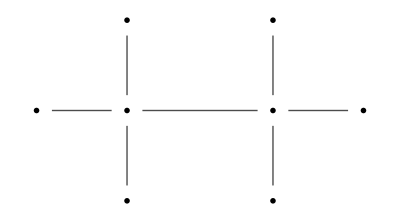
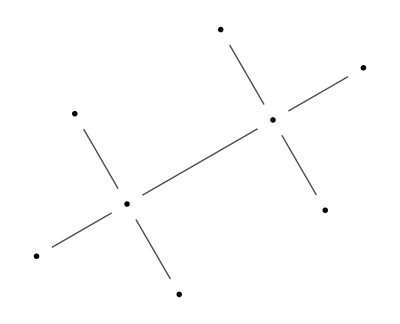
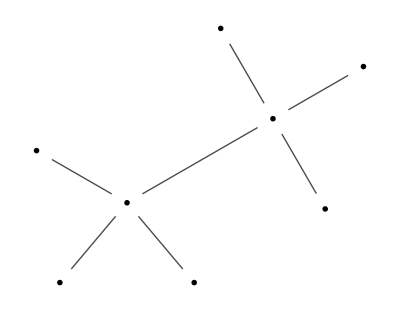
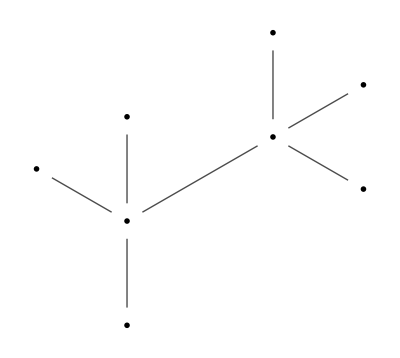
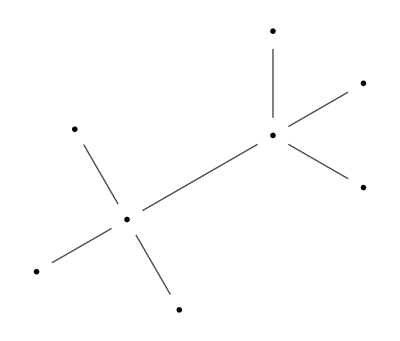
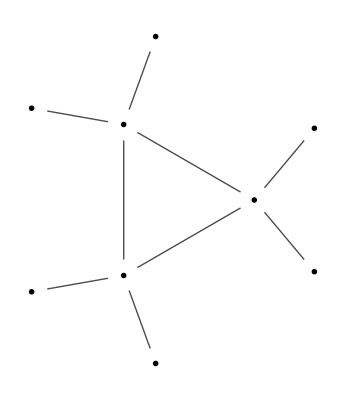
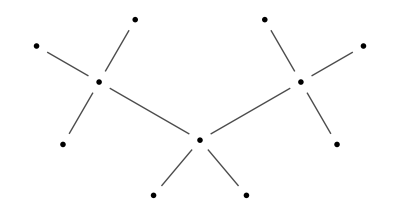
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ChemicalData[#,"StructureGraph"]&,ChemicalData["Alkanes"][[1;;20]]]
```

```mathematica
ChemicalData["Alkanes"][[1;;20]]
```

{liquid methane,methane,methane-13 C,methane-d 1,methane-d 2,methane-d 3,methane-d 4,methane-13 C,d 4,ethane,ethane-13 C1,ethane-d 1,ethane-13 C2,ethane-1,1,2,2-d 4,ethane-d 5,ethane-d 6,cyclopropane,propane,propane-1-13 C,propane-2,2-d 2,propane-1,1,1,3,3,3-d 6}

```mathematica
ChemicalData["Alkanes"][[1]]["Dataset"]
```

```mathematica
ChemicalData["Methane","Dataset"]
```

```mathematica
ChemicalData[SemanticInterpretation["methyl hidride"],"Dataset"]
```